## Create the wave function set -Graphics-

#### For a given set of {spin, M} values, generate a set of wave-functions φ_IMj=|IMK_j>

```mathematica
ClearAll["Global*`"]
```

### Constants

```mathematica
(*The spin to be tested*)
spin=3;
(*Euler Angles*)
angles={π/3,π/5,π/7};
```

### Generate the M and K values based on an index running from 1 to 2I+1

```mathematica
projections[spin_]:=Table[i,{i,-spin,spin,1}];
mvalues=projections[spin];
kvalues=projections[spin];
```

#### Create the set of states with the same M, and the same K, respectively

```mathematica
Kstates[spin_,m_]:=Table[{spin,m,k},{k,-spin,spin}];
Mstates[spin_,k_]:=Table[{spin,m,k},{m,-spin,spin}];
```

#### Create the mathematical implementation that calculates the Wigner matrix element 𝒟(IMK)

```mathematica
wdreal[i_,m_,k_,angles_]:=Re[N[WignerD[{i,m,k},angles[[1]],angles[[2]],angles[[3]]]]];
wdtable[states_,angles_]:=Table[wdreal[states[[i,1]],states[[i,2]],states[[i,3]],angles],{i,1,Length[states]}];
```

### Create tabular data points for the Wigner-D functions with all the possible K values, at given M

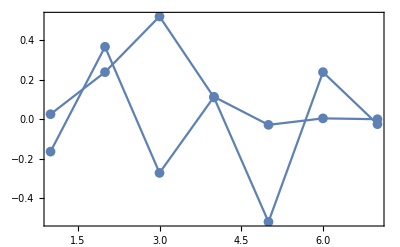

```mathematica
wdDataPointsM[m_]:=Table[{i,wdtable[Kstates[spin,m],angles][[i]]},{i,1,Length[wdtable[Kstates[spin,m],angles]]}];
t1=wdDataPointsM[mvalues[[4]]];
t2=wdDataPointsM[mvalues[[1]]];
lp[data_]:=ListPlot[data,Joined->True,PlotMarkers->{Automatic,Medium},Axes->False,Frame->True,PlotRange->Full]
Show[lp[t1],lp[t2],PlotRange->Full]
```

```mathematica
totalMdata[spin_,angles_]:=Table[wdDataPointsM[mvalues[[i]]],{i,1,Length[mvalues]}];
```

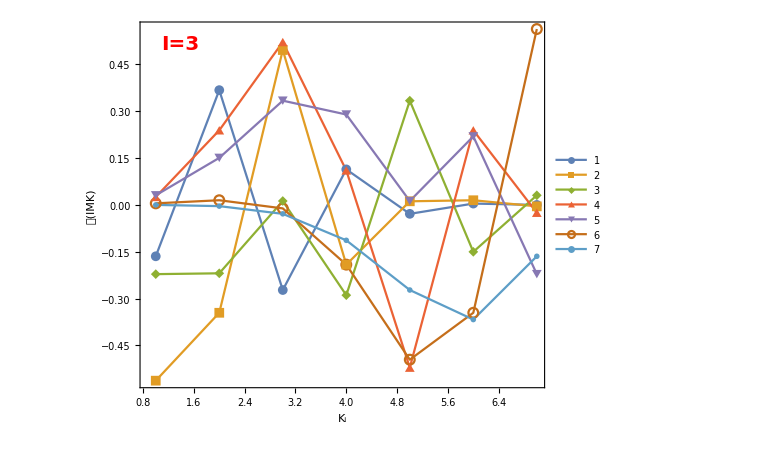

```mathematica
ListPlot[totalMdata[spin,angles],Frame->True,Axes->False,Joined->True,PlotMarkers->{Automatic, Medium},ImageSize->Large,PlotRange->Full,FrameStyle->Directive[Black,Thick],PlotLegends->Placed[Automatic,Right],Epilog->{Inset[Style[StringTemplate["I=``"][spin],Bold,Red,20,FontFamily->"Times"],Scaled[{0.1,0.94}]]},AspectRatio->0.8,FrameLabel->{"K_i","𝒟(IMK)"},LabelStyle->{19,Bold,Black,FontFamily->"Times"}]
```

## Create partial data plots for certain values of M

```mathematica
partialDataTableM[spin_,angles_,mleft_,mright_]:=Table[totalMdata[spin,angles][[i]],{i,mleft,mright}];
```

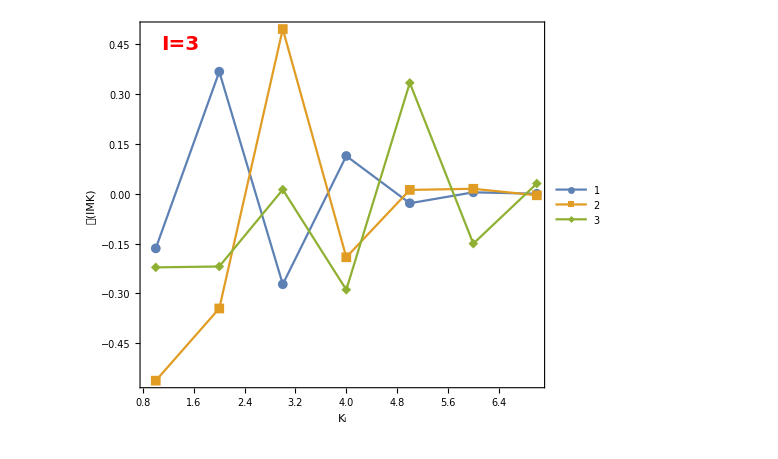

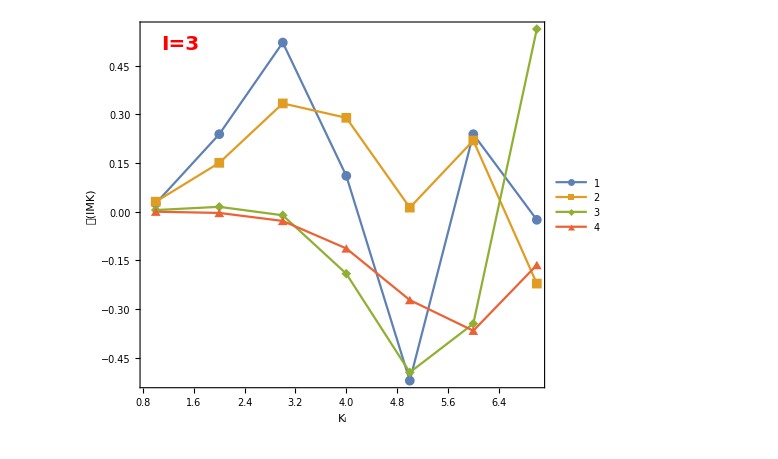

```mathematica
ListPlot[partialDataTableM[spin,angles,1,3],Frame->True,Axes->False,Joined->True,PlotMarkers->{Automatic, Medium},ImageSize->Large,PlotRange->Full,FrameStyle->Directive[Black,Thick],PlotLegends->Placed[Automatic,Right],Epilog->{Inset[Style[StringTemplate["I=``"][spin],Bold,Red,20,FontFamily->"Times"],Scaled[{0.1,0.94}]]},AspectRatio->0.8,FrameLabel->{"K_i","𝒟(IMK)"},LabelStyle->{19,Bold,Black,FontFamily->"Times"}]
ListPlot[partialDataTableM[spin,angles,4,7],Frame->True,Axes->False,Joined->True,PlotMarkers->{Automatic, Medium},ImageSize->Large,PlotRange->Full,FrameStyle->Directive[Black,Thick],PlotLegends->Placed[Automatic,Right],Epilog->{Inset[Style[StringTemplate["I=``"][spin],Bold,Red,20,FontFamily->"Times"],Scaled[{0.1,0.94}]]},AspectRatio->0.8,FrameLabel->{"K_i","𝒟(IMK)"},LabelStyle->{19,Bold,Black,FontFamily->"Times"}]
```